```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/DESI/math

```mathematica
$Assumptions={f>0,V0>0,t>0,x0>0};
```

### Eemeli

```mathematica
u1[t_]=(-Sin[(π t)/T])/Sqrt[U0/ρ-Sin[(π t)/T]^2];
u2[t_]=(-U0/ρ Cos[(π t)/T]+(π t)/T Sin[(π t)/T])/Sqrt[U0/ρ-Sin[(π t)/T]^2];
```

```mathematica
G={{u1[T],u2[T]},{u1'[T],u2'[T]}}
```

{{0,U0/(√(U0/ρ) ρ)},{π/(T √(U0/ρ)),-π^2/(T √(U0/ρ))}}

```mathematica
Simplify[Tr[G]/.{U0->ρ Tanh[x0]^2,T->(π Cosh[x0])/Sqrt[2]},{x0>0}]
```

-√2 π Csch[x0]

### H = 0

```mathematica
V[x_]=Tanh[x]^2;
```

```mathematica
dT=π/Sqrt[2(1-Tanh[x0]^2)]//Simplify
xsol[t_]=ArcSinh[Cos[(π t)/dT]/Sqrt[1/Tanh[x0]^2-1]]//Simplify
```

π/(√2 √(Sech[x0]^2))

ArcSinh[Cos[√2 t √(Sech[x0]^2)]/(√(Csch[x0]^2))]

```mathematica
xsol[0]//Simplify
xsol[dT]//Simplify
xsol'[0]
```

ArcSinh[1/(√(Csch[x0]^2))]

-ArcSinh[1/(√(Csch[x0]^2))]

0

```mathematica
Simplify[xsol''[t]+V'[xsol[t]]]
```

0

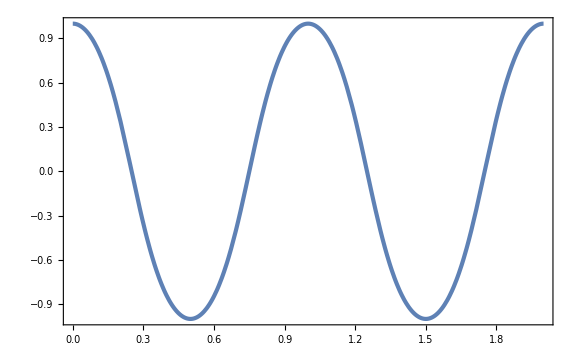

```mathematica
Plot[xsol[tp 2dT]/.{x0->1},{tp,0,2}]
```

```mathematica
V''[x]//Simplify
```

-2 (-2+Cosh[2 x]) Sech[x]^4

```mathematica
FullSimplify[u1''[t]+V''[xsol[t]]u1[t]/.{U0->ρ Tanh[x0]^2,T->(π Cosh[x0])/Sqrt[2]},{x0>0}]
```

(Cosh[2 x0] Sech[x0]^6 Sin[√2 t Sech[x0]] (2 Cos[2 √2 t Sech[x0]] (89-25 Cosh[4 x0])-8 Cos[4 √2 t Sech[x0]] (3+Cosh[4 x0])-8 (7+5 Cosh[4 x0])+4 Cos[6 √2 t Sech[x0]] Sinh[2 x0]^2))/(128 (1+Cos[√2 t Sech[x0]]^2 Sinh[x0]^2)^2 (-Sin[√2 t Sech[x0]]^2+Tanh[x0]^2)^(5/2))

```mathematica
Vpp[t_]=V''[xsol[t]]//Simplify;
```

```mathematica
VppMean=1/dT Integrate[Vpp[t],{t,0,dT}]
```

Sech[x0] (-1+3 Sech[x0]^2)

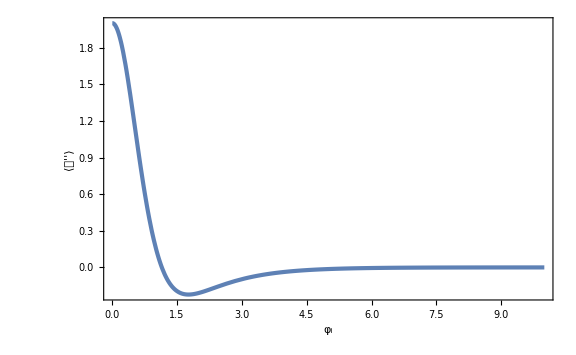

```mathematica
Plot[VppMean,{x0,0,10},PlotRange->Full,FrameLabel->{Subscript[φ, "i"],⟨𝒱''⟩}]
```

```mathematica
Integrate[(Vpp[t]-VppMean),{t,0,dT}]
```

0

```mathematica
VppVar=1/dT Integrate[Vpp[t]^2,{t,0,dT}]-VppMean^2//Simplify
```

1/8 (447+468 Cosh[x0]+92 Cosh[2 x0]+12 Cosh[3 x0]+5 Cosh[4 x0]) Sech[x0]^7 Sinh[x0/2]^4

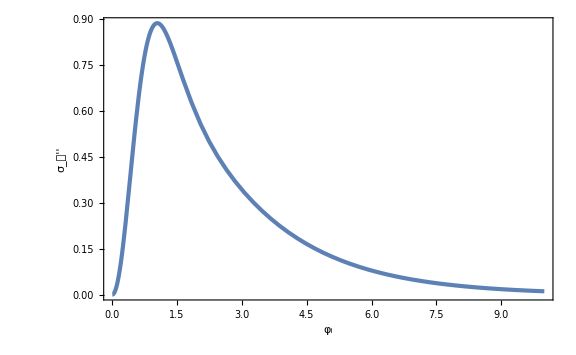

```mathematica
Plot[Sqrt[VppVar],{x0,0,10},FrameLabel->{Subscript[φ, "i"],Subscript[σ, 𝒱'']}]
```

```mathematica
psi[t_]=(Vpp[t]-VppMean)/Sqrt[2VppVar]//Simplify;
```

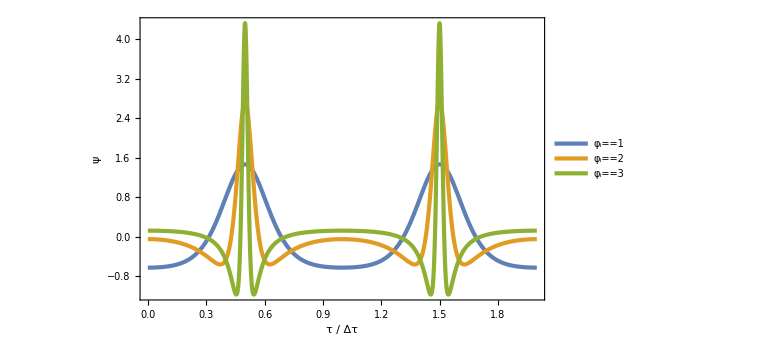

```mathematica
Plot[{psi[tp dT]/.{x0->1},psi[tp dT]/.{x0->2},psi[tp dT]/.{x0->3}},{tp,0,2},PlotRange->Full,FrameLabel->{"τ / Δτ",ψ},PlotLegends->Placed[{Subscript[φ, "i"]==1,Subscript[φ, "i"]==2,Subscript[φ, "i"]==3},{0.5,0.7}]]
```

```mathematica
x0s=1;
FloquetList=Flatten[ParallelTable[u1sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==1,u'[0]==0}/.{x0->x0s},{u[t],u'[t]},{t,0,dT/.{x0->x0s}}][[1]];
u2sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==0,u'[0]==1}/.{x0->x0s},{u[t],u'[t]},{t,0,dT/.{x0->x0s}}][[1]];
w[t_]=Transpose[{{u[t],u'[t]}/.u1sol,{u[t],u'[t]}/.u2sol}];
{Ak,q,Re[ArcCosh[1/2 Tr[w[dT]/.{x0->x0s}]]]},{Ak,-0.5,5,10^-2},{q,0,1,10^-2}],1];//AbsoluteTiming
FloquetFig=ListDensityPlot[FloquetList,PlotRange->Full,PlotLegends->BarLegend[Automatic,LegendLabel->Placed["μ_k Δτ",Right]],FrameLabel->{{OverTilde[q],None},{Subscript[A, k],Subscript[φ, "i"]==x0s}},GridLines->{None,{Sqrt[VppVar/2]/.{x0->x0s}}},GridLinesStyle->Directive[Black,Dashed,AbsoluteThickness[3]]]
Export["Floquet_xi="<>ToString[x0s]<>".pdf",FloquetFig,ImageResolution->300];
```

{10.7881,Null}

-Graphics-

```mathematica
x0s=2;
FloquetList=Flatten[ParallelTable[u1sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==1,u'[0]==0}/.{x0->x0s},{u[t],u'[t]},{t,0,dT/.{x0->x0s}}][[1]];
u2sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==0,u'[0]==1}/.{x0->x0s},{u[t],u'[t]},{t,0,dT/.{x0->x0s}}][[1]];
w[t_]=Transpose[{{u[t],u'[t]}/.u1sol,{u[t],u'[t]}/.u2sol}];
{Ak,q,Re[ArcCosh[1/2 Tr[w[dT]/.{x0->x0s}]]]},{Ak,-0.5,5,10^-2},{q,0,1,10^-2}],1];//AbsoluteTiming
FloquetFig=ListDensityPlot[FloquetList,PlotRange->Full,PlotLegends->BarLegend[Automatic,LegendLabel->Placed["μ_k Δτ",Right]],FrameLabel->{{OverTilde[q],None},{Subscript[A, k],Subscript[φ, "i"]==x0s}},GridLines->{None,{Sqrt[VppVar/2]/.{x0->x0s}}},GridLinesStyle->Directive[Black,Dashed,AbsoluteThickness[3]]]
Export["Floquet_xi="<>ToString[x0s]<>".pdf",FloquetFig,ImageResolution->300];
```

{11.594,Null}

-Graphics-

```mathematica
x0s=3;
FloquetList=Flatten[ParallelTable[u1sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==1,u'[0]==0}/.{x0->x0s},{u[t],u'[t]},{t,0,dT/.{x0->x0s}}][[1]];
u2sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==0,u'[0]==1}/.{x0->x0s},{u[t],u'[t]},{t,0,dT/.{x0->x0s}}][[1]];
w[t_]=Transpose[{{u[t],u'[t]}/.u1sol,{u[t],u'[t]}/.u2sol}];
{Ak,q,Re[ArcCosh[1/2 Tr[w[dT]/.{x0->x0s}]]]},{Ak,-0.5,5,10^-2},{q,0,1,10^-2}],1];//AbsoluteTiming
FloquetFig=ListDensityPlot[FloquetList,PlotRange->Full,PlotLegends->BarLegend[Automatic,LegendLabel->Placed["μ_k Δτ",Right]],FrameLabel->{{OverTilde[q],None},{Subscript[A, k],Subscript[φ, "i"]==x0s}},GridLines->{None,{Sqrt[VppVar/2]/.{x0->x0s}}},GridLinesStyle->Directive[Black,Dashed,AbsoluteThickness[3]]]
Export["Floquet_xi="<>ToString[x0s]<>".pdf",FloquetFig,ImageResolution->300];
```

{13.7514,Null}

-Graphics-

```mathematica
FloquetFunc=Flatten[ParallelTable[u1sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==1,u'[0]==0}/.{Ak->k^2+VppMean,q->Sqrt[VppVar/2]},{u[t],u'[t]},{t,0,dT}][[1]];
u2sol=NDSolve[{u''[t]+(Ak-2q psi[t])u[t]==0,u[0]==0,u'[0]==1}/.{Ak->k^2+VppMean,q->Sqrt[VppVar/2]},{u[t],u'[t]},{t,0,dT}][[1]];
w[t_]=Transpose[{{u[t],u'[t]}/.u1sol,{u[t],u'[t]}/.u2sol}];
{k,x0,Re[ArcCosh[1/2 Tr[w[dT]/.{x0->x0s}]]]},{x0,1,3,10^-2},{k,0,3,10^-2}],1];//AbsoluteTiming
```

{14.8106,Null}

```mathematica
FloquetFuncFig=ListDensityPlot[FloquetFunc,FrameLabel->{k,Subscript[φ, "i"]},PlotLegends->BarLegend[Automatic,LegendLabel->Placed["μ_k Δτ",Right]],PlotRange->Full]
```

-Graphics-

```mathematica
Export["Floquet.pdf",FloquetFuncFig,ImageResolution->300];
```

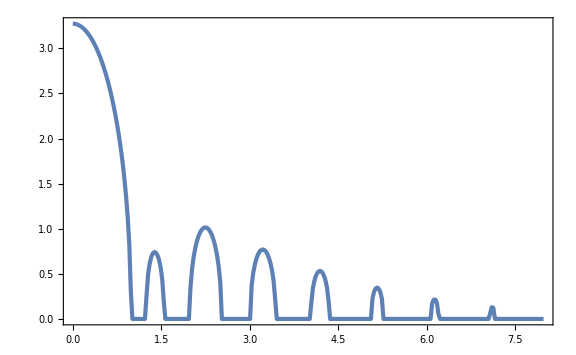

```mathematica
ListPlot[Map[{#[[1]]dT/π/.{x0->2},#[[3]]}&,Select[FloquetFunc,#[[2]]==2&]],PlotRange->Full]
```

### w/ DM

```mathematica
f=10^-3;
h=0.674;
Ωm=0.3;
ρm0=3 h^2 Ωm;
V0=1.1 3(1-Ωm)h^2;
xi=7.35f;
zi=1000;
mth=Sqrt[V0]/f
```

1024.39

```mathematica
V[x_]=V0 Tanh[x/f]^2;
H[x_,p_,z_]=Sqrt[(p^2/2+V[x]+ρm0(1+z)^3)/3];
```

```mathematica
Hi=H[xi,0,zi];
tf=20000/Hi;
```

```mathematica
txmax={};
txzero={};
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t],z[t]]x'[t]+V'[x[t]]==0,z'[t]==-(1+z[t])H[x[t],x'[t],z[t]],x[0]==xi,x'[0]==0,z[0]==zi,WhenEvent[x'[t]==0,AppendTo[txmax,t]],WhenEvent[x[t]==0,AppendTo[txzero,t]],WhenEvent[z[t]==0,t0=t]},{x[t],x'[t],z[t]},{t,0,tf}(*,WorkingPrecision->50,MaxSteps->1000000*)][[1]];
```

```mathematica
xsol[t_]=x[t]/.bgsol;
psol[t_]=x'[t]/.bgsol;
zsol[t_]=z[t]/.bgsol;
Hsol[t_]=H[xsol[t],psol[t],zsol[t]];
wsol[t_]=(psol[t]^2/2-V[xsol[t]])/(psol[t]^2/2+V[xsol[t]]);
Vppsol[t_]=V''[xsol[t]];
dTList=Differences[txmax];
```

```mathematica
VppMeanList=Table[1/dTList[[i]] NIntegrate[Vppsol[t]/mth^2,{t,txmax[[i]],txmax[[i+1]]}],{i,Length[dTList]}];
```

```mathematica
VppVarList=Table[1/dTList[[i]] NIntegrate[Vppsol[t]^2/mth^4,{t,txmax[[i]],txmax[[i+1]]}]-VppMeanList[[i]]^2,{i,Length[dTList]}];
```

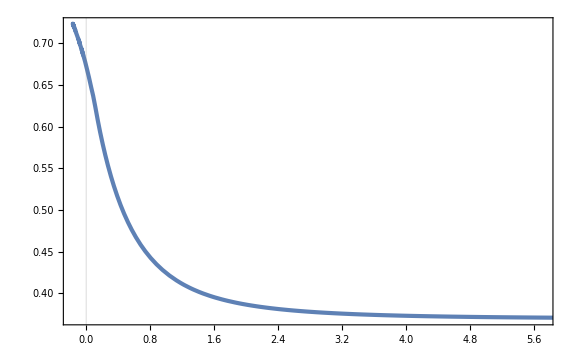

```mathematica
ParametricPlot[{zsol[t],(1+zsol[t])^(-3/2)Hsol[t]},{t,0,tf},GridLines->{{0},None}]
```

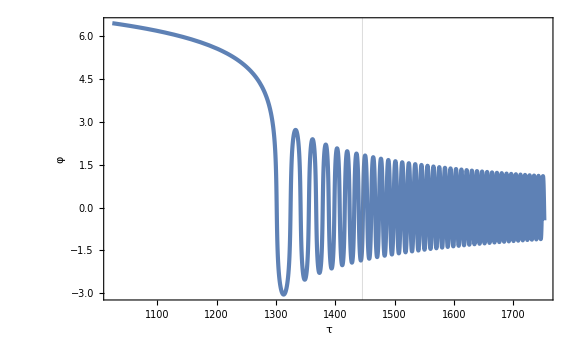

```mathematica
Plot[xsol[tp/mth]/f,{tp,mth,tf mth},PlotRange->Full,GridLines->{{mth t0},None},FrameLabel->{τ,φ}]
```

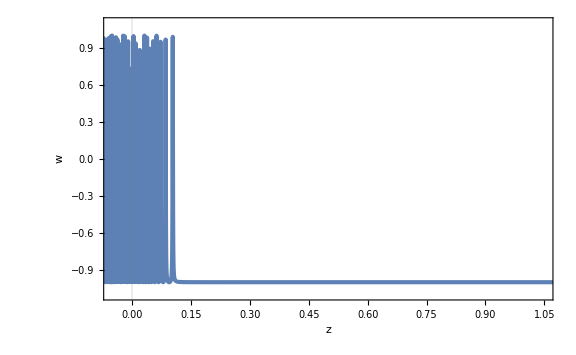

```mathematica
ParametricPlot[{zsol[t],wsol[t]},{t,0,tf},PlotRange->{{-0.05,1.05},{-1.1,1.1}},FrameLabel->{z,w},GridLines->{{0},None}]
```

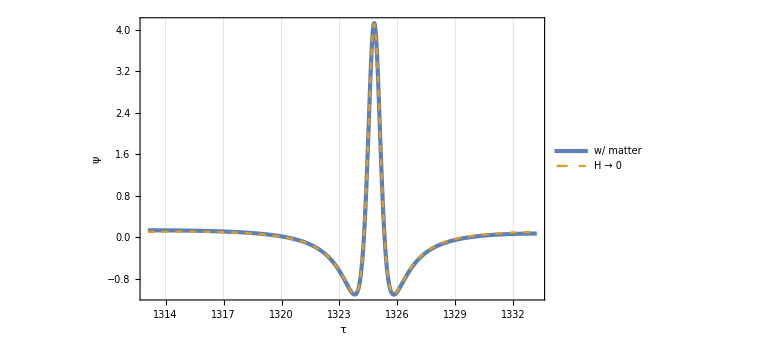

```mathematica
is=1;
Plot[{(Vppsol[tp/mth]/mth^2-VppMeanList[[is]])/Sqrt[2VppVarList[[is]]],psi[tp-mth txzero[[is+1]]+1/2 dT]/.{x0->(Abs[xsol[txmax[[is]]]]+Abs[xsol[txmax[[is+1]]]])/(2f)}},{tp,mth txmax[[is]],mth txmax[[is+1]]},PlotRange->Full,GridLines->{txzero,None},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{ψ,None},{τ,"Oscillation "<>ToString[is]}},PlotLegends->Placed[{"w/ matter","H → 0"},{0.2,0.8}]]
```

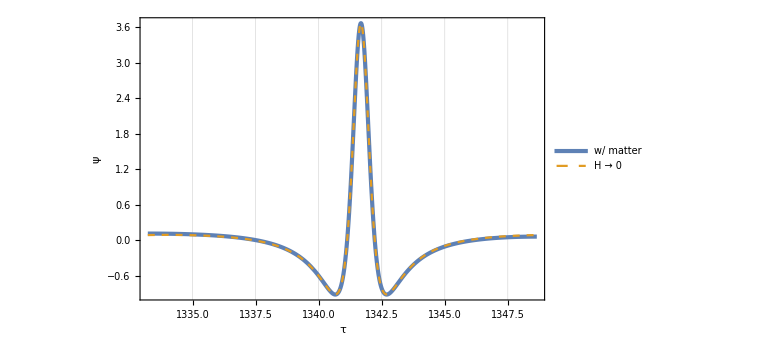

```mathematica
is=2;
Plot[{(Vppsol[tp/mth]/mth^2-VppMeanList[[is]])/Sqrt[2VppVarList[[is]]],psi[tp-mth txzero[[is+1]]+1/2 dT]/.{x0->(Abs[xsol[txmax[[is]]]]+Abs[xsol[txmax[[is+1]]]])/(2f)}},{tp,mth txmax[[is]],mth txmax[[is+1]]},PlotRange->Full,GridLines->{txzero,None},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{ψ,None},{τ,"Oscillation "<>ToString[is]}},PlotLegends->Placed[{"w/ matter","H → 0"},{0.2,0.8}]]
```

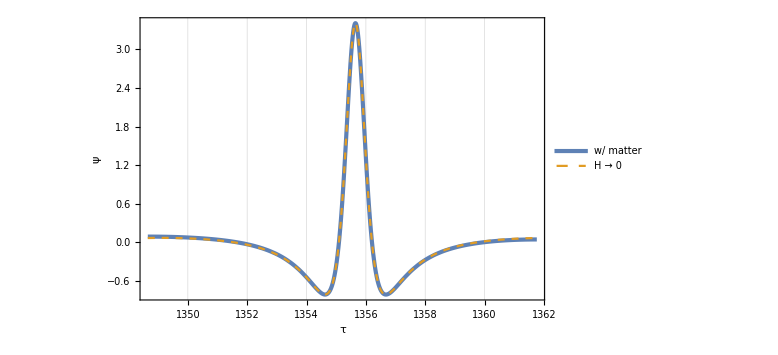

```mathematica
is=3;
Plot[{(Vppsol[tp/mth]/mth^2-VppMeanList[[is]])/Sqrt[2VppVarList[[is]]],psi[tp-mth txzero[[is+1]]+1/2 dT]/.{x0->(Abs[xsol[txmax[[is]]]]+Abs[xsol[txmax[[is+1]]]])/(2f)}},{tp,mth txmax[[is]],mth txmax[[is+1]]},PlotRange->Full,GridLines->{txzero,None},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{ψ,None},{τ,"Oscillation "<>ToString[is]}},PlotLegends->Placed[{"w/ matter","H → 0"},{0.2,0.8}]]
```

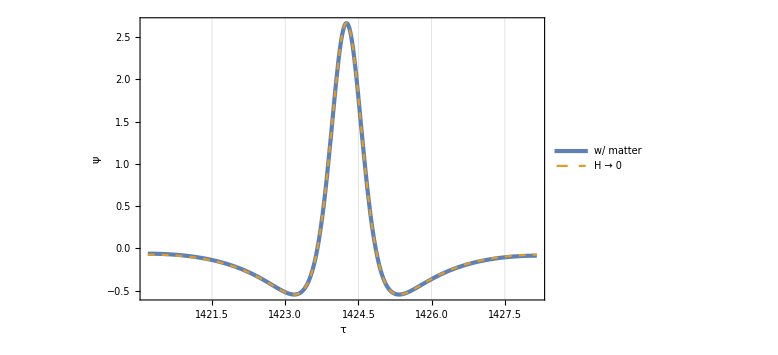

```mathematica
is=10;
Plot[{(Vppsol[tp/mth]/mth^2-VppMeanList[[is]])/Sqrt[2VppVarList[[is]]],psi[tp-mth txzero[[is+1]]+1/2 dT]/.{x0->(Abs[xsol[txmax[[is]]]]+Abs[xsol[txmax[[is+1]]]])/(2f)}},{tp,mth txmax[[is]],mth txmax[[is+1]]},PlotRange->Full,GridLines->{txzero,None},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{ψ,None},{τ,"Oscillation "<>ToString[is]}},PlotLegends->Placed[{"w/ matter","H → 0"},{0.2,0.8}]]
```

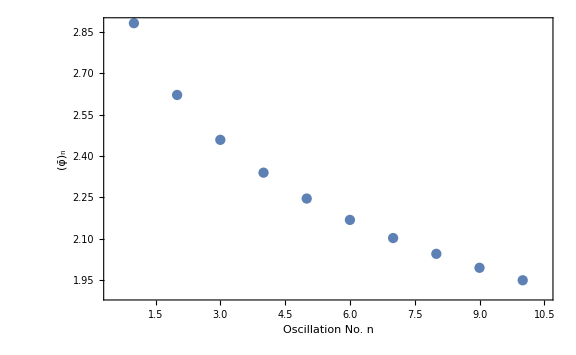

```mathematica
ListPlot[Table[{i,(Abs[xsol[txmax[[i]]]]+Abs[xsol[txmax[[i+1]]]])/(2f)},{i,1,10}],Joined->False,PlotRange->{{0.5,10.5},Full},FrameLabel->{"Oscillation No. n",Subscript[OverBar[φ], n]}]
```

```mathematica
((1+zsol[txmax[[1]]])/(1+zsol[txmax[[1+1]]]))^(3/2)
```

1.02151

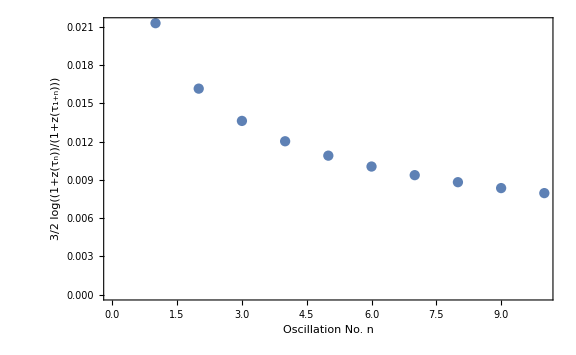

```mathematica
ListPlot[Table[{i,Log[((1+zsol[txmax[[i]]])/(1+zsol[txmax[[i+1]]]))^(3/2)]},{i,1,10}],Joined->False,FrameLabel->{"Oscillation No. n",3/2 Log[(1+z[Subscript[τ, n]])/(1+z[Subscript[τ, n+1]])]}]
```

```mathematica
mth dTList[[1]]
(Abs[xsol[txmax[[1]]]]+Abs[xsol[txmax[[2]]]])/(2f)
dT/.{x0->(Abs[xsol[txmax[[1]]]]+Abs[xsol[txmax[[2]]]])/(2f)}
((dT/.{x0->xsol[txmax[[1]]]/f})+(dT/.{x0->xsol[txmax[[2]]]/f}))/2
```

20.1483

2.88084

19.8656

20.1348

```mathematica
dT
```

(π Cosh[x0])/(√2)

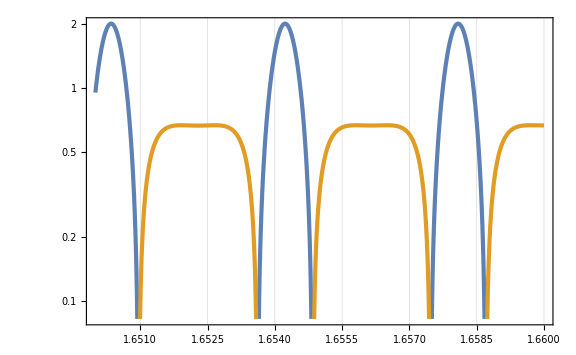

```mathematica
LogPlot[{Vppsol[t]/mth^2,-Vppsol[t]/mth^2},{t,1.65,1.66},GridLines->{tVppmax,None}]
```

```mathematica
TList=Table[mth(tVppmax[[i+1]]-tVppmax[[i]]),{i,Length[tVppmax]-1}]
```

{23.3954,16.8741,13.9723,12.2407,11.0589,10.1871,9.51008,8.96482,8.51363,8.13236,7.80472,7.51929,7.26774,7.04394,6.84314,6.6617,6.49672,6.34587,6.20727,6.07937,5.96085,5.85066,5.74786,5.65168,5.56144,5.47657,5.39656,5.32097,5.24942,5.18156,5.1171,5.05576,4.9973,4.94151,4.88819,4.83719,4.78832,4.74145,4.69645,4.65321,4.61161,4.57156,4.53296,4.49573,4.4598,4.42508,4.39153,4.35906,4.32764,4.2972,4.2677,4.23909,4.21132,4.18437,4.15819,4.13274,4.10799,4.08392,4.06049,4.03768,4.01546,3.99381,3.97269,3.9521,3.93201,3.91241,3.89327,3.87457,3.85631,3.83846,3.821,3.80394,3.78725,3.77091,3.75493,3.73928,3.72395,3.70894}

```mathematica
VppMeanList=Table[1/(tVppmax[[i+1]]-tVppmax[[i]])NIntegrate[Vppsol[t],{t,tVppmax[[i]],tVppmax[[i+1]]}],{i,Length[tVppmax]-1}];//AbsoluteTiming
```

{11.147,Null}

```mathematica
qList=Table[1/(tVppmax[[i+1]]-tVppmax[[i]])NIntegrate[(Vppsol[t]-VppMeanList[[i]])^2/(2 m2^2),{t,tVppmax[[i]],tVppmax[[i+1]]}],{i,Length[tVppmax]-1}];//AbsoluteTiming
```

{13.2172,Null}

```mathematica
qList
```

{0.0140528,0.0193526,0.0233856,0.0267996,0.0298346,0.0326074,0.0351844,0.0376071,0.0399026,0.0420899,0.0441829,0.0461918,0.0481247,0.0499877,0.0517861,0.0535239,0.0552045,0.056831,0.0584059,0.0599313,0.0614094,0.0628418,0.0642302,0.065576,0.0668807,0.0681455,0.0693715,0.0705598,0.0717114,0.0728276,0.0739091,0.0749568,0.0759716,0.0769544,0.077906,0.078827,0.0797184,0.0805809,0.0814151,0.0822216,0.0830011,0.0837544,0.084482,0.0851846,0.0858627,0.0865169,0.0871479,0.087756,0.0883419,0.0889062,0.0894492,0.0899715,0.0904737,0.0909561,0.0914192,0.0918636,0.0922895,0.0926975,0.093088,0.0934614,0.0938181,0.0941585,0.0944829,0.0947919,0.0950856,0.0953646,0.095629,0.0958793,0.0961158,0.0963389,0.0965488,0.0967459,0.0969305,0.0971028,0.0972632,0.097412,0.0975494,0.0976757}